### In this notebook we will derive the variable step size BDFL3_2 (and hopefully also BDFL4_2 and 5_2) via the interpolating method

#### As a test run, we will derive the BDF2 method with the approach of Arevalo and Soderlind

#### Let P(t_n) be some polynomial at time t_n where P'(t_n)=f(t_n,P(t_n)) (a) We add these conditions: s_(n-1)cos(θ_0)+h s'_(n-1)sin(θ_0)=0 and s_(n-2)cos(θ_1)+h s'_(n-2)sin(θ_1)=0 where s_n=P(t_n)-y_n We have tan(θ)=0, sin(θ)=0, cos(θ)=1. Plugging this into the two previous equations we have s_(n-1)=0 and s_(n-2)=0. This means P(t_(n-1))=y_(n-1) and P(t_(n-2))=y_(n-2). Let’s call these equations (b) and (c), respectively. These conditions determine a polynomial P(t) (quadratic). Then the value P(t_n) gives the updated solution. For convenience, we write the polynomial in the form: P(t)=a+(b(t-t_n))^2+(t-t_n)F_n where P'(t_n)=F_n We then solve for (a)-(c), with the notation that t_n=t_(n-1)+h_(n-1): P(t_n)=a P(t_(n-1))=a+h_(n-1)^2 b-h_(n-1)F_n⧦y_(n-1) P(t_(n-2))=a+(h_(n-2)+h_(n-1))^2 b-(h_(n-2)+h_(n-1))F_n⧦y_(n-2) Let’s now take the difference of y_(n-2)-y_(n-1) b(2 h_(n-2)h_(n-1)+h_(n-2)^2)-h_(n-2)F_n=y_(n-2)-y_(n-1) b=(y_(n-2)-y_(n-1)+h_(n-2)F_n)/(h_(n-2)^2+2 h_(n-2)h_(n-1)) Note that from the P(t_(n-1)) equation, a=y_(n-1)+h_(n-1)F_n-h_(n-1)^2 b Therefore, a=y_(n-1)+h_(n-1)F_n-h_(n-1)^2((y_(n-2)-y_(n-1)+h_(n-2)F_n)/(h_(n-2)^2+2 h_(n-2)h_(n-1))) If we assume a constant step size case: h_(n-1)=h_(n-2)=h a=y_(n-1)+h F_n-1/3(y_(n-2)-y_(n-1)+h F_n)=4/3 y_(n-1)-1/3 y_(n-2)+2/3 h F_n If we let a=y_n, then we have the BDF2 method Let’s also make sure that we got the correct variable step size BDF2. Let ω_n=(h_(n-1))/(h_(n-2)).

```mathematica
Subscript[y, n-1]+Subscript[h, n-1] Subscript[F, n]-Subscript[h, n-1]^2((Subscript[y, n-2]-Subscript[y, n-1]+Subscript[h, n-2] Subscript[F, n])/(Subscript[h, n-2]^2+2 Subscript[h, n-2] Subscript[h, n-1]))/.{Subscript[h, n-2]->Subscript[h, n-1]/Subscript[ω, n]}//Simplify
```

(-y_(-2+n) ω_n^2+F_n h_(-1+n) (1+ω_n)+y_(-1+n) (1+ω_n)^2)/(1+2 ω_n)

```mathematica
Collect[(-Subscript[y, -2+n] Subscript[ω, n]^2+Subscript[F, n] Subscript[h, -1+n] (1+Subscript[ω, n])+Subscript[y, -1+n] (1+Subscript[ω, n])^2)/(1+2 Subscript[ω, n]),{Subscript[y, n-2],Subscript[y, n-1],Subscript[h, n-1] Subscript[F, n]}]
```

-(y_(-2+n) ω_n^2)/(1+2 ω_n)+(F_n h_(-1+n) (1+ω_n))/(1+2 ω_n)+(y_(-1+n) (1+ω_n)^2)/(1+2 ω_n)

#### These coefficients above match the ones found in HNW I, Section III.5 (page 401)

#### Now we want to find BDFL3_2. This is a 3-step, 2^nd order LMM. We therefore need to impose 3 conditions to determine the method. We will therefore impose this generalization: The degree of P corresponds to the order of the method One condition is that P'(t_n)=F_n (1) The other two conditions will come from two independent linear combinations of: P(t_(n-1))=y_(n-1) P(t_(n-2))=y_(n-2) P(t_(n-3))=y_(n-3) To make this happen, say we have: θ P(t_(n-1))+(1-θ)P(t_(n-2))=θ y_(n-1)+(1-θ)y_(n-2) (2) γ P(t_(n-2))+(1-γ)P(t_(n-3))=γ y_(n-2)+(1-γ)y_(n-3) (3) We also let: P(t)=a+(b(t-t_n))^2+(t-t_n)F_n This allows once again P(t_n)=a We then solve (1)-(3) for the value of P(t_n)=a, then choose θ and γ such that the formula for a matches BDFL3_2 for fixed step size. We then expand it into variable step size using the values of θ and γ

#### Let’s set up the formula for this. For the input code, note that P(t_(n-1))=Ptn1, y_(n-1)=yn1, and so forth

```mathematica
Solve[θ Ptn1+(1-θ)Ptn2==θ yn1+(1-θ)yn2,Ptn1]//Simplify
```

{{Ptn1→yn1+yn2 (-1+1/θ)+(Ptn2 (-1+θ))/θ}}

#### Note that this means that yn2 (-1+1/θ)+(Ptn2 (-1+θ))/θ must equal 0

```mathematica
Solve[yn2 (-1+1/θ)+(Ptn2 (-1+θ))/θ==0,Ptn2]//Simplify
```

{{Ptn2→yn2}}

#### This is consistent, meaning we are free to chose any value of θ except 0. Let’s also check γ

```mathematica
Solve[γ Ptn2+(1-γ)Ptn3==γ yn2+(1-γ)yn3,Ptn3]//Simplify
```

{{Ptn3→yn3+((Ptn2-yn2) γ)/(-1+γ)}}

```mathematica
Solve[((Ptn2-yn2) γ)/(-1+γ)==0,Ptn2]
```

{{Ptn2→yn2}}

#### We are free then to use any value of γ except 1. For now let’s try γ=0

```mathematica
γ Ptn2+(1-γ)Ptn3==γ yn2+(1-γ)yn3/.γ->0
```

Ptn3==yn3

#### Now we define P as a function of t. Here we will go back to the original notation (Ptn1->P(t_(n-1)))

```mathematica
ClearAll["`*"]
```

```mathematica
P[t1_]:=a+b(t1-Subscript[t, n])^2+(t1-Subscript[t, n])Subscript[F, n]
```

```mathematica
eq1=P[Subscript[t, n-1]]==Subscript[y, n-1]
eq2=P[Subscript[t, n-2]]==Subscript[y, n-2]
eq3=P[Subscript[t, n-3]]==Subscript[y, n-3]
```

a+F_n (t_(-1+n)-t_n)+b (t_(-1+n)-t_n)^2==y_(-1+n)

a+F_n (t_(-2+n)-t_n)+b (t_(-2+n)-t_n)^2==y_(-2+n)

a+F_n (t_(-3+n)-t_n)+b (t_(-3+n)-t_n)^2==y_(-3+n)

#### Let’s clean it up a bit by introducing step size: t_n=t_(n-1)+h_(n-1)

```mathematica
eq1=eq1/.(Subscript[t, n-1]-Subscript[t, n])->-Subscript[h, n-1]
eq2=eq2/.(Subscript[t, n-2]-Subscript[t, n])->-Subscript[h, n-1]-Subscript[h, n-2]
eq3=eq3/.(Subscript[t, n-3]-Subscript[t, n])->-Subscript[h, n-1]-Subscript[h, n-2]-Subscript[h, n-3]
```

a-F_n h_(-1+n)+b h_(-1+n)^2==y_(-1+n)

a+F_n (-h_(-2+n)-h_(-1+n))+b (-h_(-2+n)-h_(-1+n))^2==y_(-2+n)

a+F_n (-h_(-3+n)-h_(-2+n)-h_(-1+n))+b (-h_(-3+n)-h_(-2+n)-h_(-1+n))^2==y_(-3+n)

#### By choice of the author of this notebook, we will use the difference of the second and third equation to find b

```mathematica
setup=Thread[Subtract @@ ({eq3, eq2} /. Equal -> List)]
```

{-F_n (-h_(-2+n)-h_(-1+n))-b (-h_(-2+n)-h_(-1+n))^2+F_n (-h_(-3+n)-h_(-2+n)-h_(-1+n))+b (-h_(-3+n)-h_(-2+n)-h_(-1+n))^2,y_(-3+n)-y_(-2+n)}

```mathematica
eqdiff=setup[[1]]==setup[[2]]
```

-F_n (-h_(-2+n)-h_(-1+n))-b (-h_(-2+n)-h_(-1+n))^2+F_n (-h_(-3+n)-h_(-2+n)-h_(-1+n))+b (-h_(-3+n)-h_(-2+n)-h_(-1+n))^2==y_(-3+n)-y_(-2+n)

```mathematica
bcheck=Solve[eqdiff,b]//Simplify
```

{{b→(F_n h_(-3+n)+y_(-3+n)-y_(-2+n))/(h_(-3+n) (h_(-3+n)+2 (h_(-2+n)+h_(-1+n))))}}

```mathematica
bval=b/.Flatten@bcheck//Simplify
```

(F_n h_(-3+n)+y_(-3+n)-y_(-2+n))/(h_(-3+n) (h_(-3+n)+2 (h_(-2+n)+h_(-1+n))))

#### Let’s now replace P(t_(n-1)) with what we found for b and solve for a in terms of θ and everything else

```mathematica
test=eq1/.Subscript[y, n-1]->(Subscript[y, n-1]+Subscript[y, n-2] (-1+1/θ)+(P[Subscript[t, n-2]] (-1+θ))/θ)/.(Subscript[t, n-2]-Subscript[t, n])->-Subscript[h, n-1]-Subscript[h, n-2]//Simplify
```

a+b h_(-1+n)^2==F_n h_(-1+n)+((-1+θ) (a-F_n (h_(-2+n)+h_(-1+n))+b (h_(-2+n)+h_(-1+n))^2))/θ+(-1+1/θ) y_(-2+n)+y_(-1+n)

```mathematica
result=a/.Flatten@Solve[test/.b->bval,a]//Simplify
```

θ F_n h_(-1+n)-(-1+θ) F_n (h_(-2+n)+h_(-1+n))-(θ h_(-1+n)^2 (F_n h_(-3+n)+y_(-3+n)-y_(-2+n)))/(h_(-3+n) (h_(-3+n)+2 (h_(-2+n)+h_(-1+n))))+((-1+θ) (h_(-2+n)+h_(-1+n))^2 (F_n h_(-3+n)+y_(-3+n)-y_(-2+n)))/(h_(-3+n) (h_(-3+n)+2 (h_(-2+n)+h_(-1+n))))-(-1+θ) y_(-2+n)+θ y_(-1+n)

```mathematica
Collect[result,{Subscript[F, n],Subscript[y, n-1],Subscript[y, n-2],Subscript[y, n-3]}]
```

F_n (θ h_(-1+n)+(1-θ) (h_(-2+n)+h_(-1+n))-(θ h_(-1+n)^2)/(h_(-3+n)+2 (h_(-2+n)+h_(-1+n)))+((-1+θ) (h_(-2+n)+h_(-1+n))^2)/(h_(-3+n)+2 (h_(-2+n)+h_(-1+n))))+(-(θ h_(-1+n)^2)/(h_(-3+n) (h_(-3+n)+2 (h_(-2+n)+h_(-1+n))))+((-1+θ) (h_(-2+n)+h_(-1+n))^2)/(h_(-3+n) (h_(-3+n)+2 (h_(-2+n)+h_(-1+n))))) y_(-3+n)+(1-θ+(θ h_(-1+n)^2)/(h_(-3+n) (h_(-3+n)+2 (h_(-2+n)+h_(-1+n))))+((1-θ) (h_(-2+n)+h_(-1+n))^2)/(h_(-3+n) (h_(-3+n)+2 (h_(-2+n)+h_(-1+n))))) y_(-2+n)+θ y_(-1+n)

#### Let’s simplify this by assuming fixed step sizes, meaning h_(n-3)=h_(n-2)=h_(n-1)=h

```mathematica
resultfixed=result/.{Subscript[h, n-3]->h,Subscript[h, n-2]->h,Subscript[h, n-1]->h}
```

-2 h (-1+θ) F_n+h θ F_n+4/5 (-1+θ) (h F_n+y_(-3+n)-y_(-2+n))-1/5 θ (h F_n+y_(-3+n)-y_(-2+n))-(-1+θ) y_(-2+n)+θ y_(-1+n)

```mathematica
Collect[resultfixed,{Subscript[F, n],Subscript[y, n-1],Subscript[y, n-2],Subscript[y, n-3]}]
```

(-6/5 h (-1+θ)+(4 h θ)/5) F_n+(4/5 (-1+θ)-θ/5) y_(-3+n)+(-9/5 (-1+θ)+θ/5) y_(-2+n)+θ y_(-1+n)

#### Looking at y_(n-1), the only coefficient next to it is θ. This means that if we want the BDFL3_2 method, θ=-α_2=3/2. Let’s see if the rest of the coefficients check out:

```mathematica
finalresultfixed=resultfixed/.θ->3/2
```

(h F_n)/2+1/10 (h F_n+y_(-3+n)-y_(-2+n))-(y_(-2+n))/2+(3 y_(-1+n))/2

```mathematica
Collect[finalresultfixed,{Subscript[F, n],Subscript[y, n-1],Subscript[y, n-2],Subscript[y, n-3]}]
```

(3 h F_n)/5+(y_(-3+n))/10-(3 y_(-2+n))/5+(3 y_(-1+n))/2

#### This is the BDFL3_2 method. However, this would require α_2 to be a fixed coefficient in the variable step size BDFL3_2

#### Let’s see what the variable step method looks like, and introduce the step size ratio ω_n=h_n/(h_(n-1))

```mathematica
varresult=result/.Subscript[h, n-3]->Subscript[h, n-2]/Subscript[ω, n-1]/.Subscript[h, n-2]->Subscript[h, n-1]/Subscript[ω, n]/.θ->3/2//Simplify
```

(F_n h_(-1+n) (-1+2 ω_n+ω_(-1+n) (-1+4 ω_n+2 ω_n^2))+ω_n (y_(-3+n) ω_(-1+n)^2 (1+2 ω_n-2 ω_n^2)+y_(-1+n) (3+6 ω_(-1+n) (1+ω_n))+y_(-2+n) (-1-2 ω_(-1+n) (1+ω_n)+ω_(-1+n)^2 (-1-2 ω_n+2 ω_n^2))))/(2 ω_n (1+2 ω_(-1+n) (1+ω_n)))

```mathematica
Collect[varresult,{Subscript[F, n],Subscript[y, n-1],Subscript[y, n-2],Subscript[y, n-3]}]
```

(y_(-3+n) ω_(-1+n)^2 (1+2 ω_n-2 ω_n^2))/(2 (1+2 ω_(-1+n) (1+ω_n)))+(y_(-1+n) (3+6 ω_(-1+n) (1+ω_n)))/(2 (1+2 ω_(-1+n) (1+ω_n)))+(y_(-2+n) (-1-2 ω_(-1+n) (1+ω_n)+ω_(-1+n)^2 (-1-2 ω_n+2 ω_n^2)))/(2 (1+2 ω_(-1+n) (1+ω_n)))+(F_n h_(-1+n) (-1+2 ω_n+ω_(-1+n) (-1+4 ω_n+2 ω_n^2)))/(2 ω_n (1+2 ω_(-1+n) (1+ω_n)))

#### As it turns out, α_2 is not necessarily fixed. Let’s check the results for fixed step size

```mathematica
Collect[varresult/.{Subscript[ω, n]->1,Subscript[ω, n-1]->1},{Subscript[F, n],Subscript[y, n-1],Subscript[y, n-2],Subscript[y, n-3]}]
```

3/5 F_n h_(-1+n)+(y_(-3+n))/10-(3 y_(-2+n))/5+(3 y_(-1+n))/2

#### FYI, α_2 in this setup can be simplified to -2/3

#### Our list of α coefficients is now, starting with α_0: {-(ω_(-1+n)^2 (1+2 ω_n-2 ω_n^2))/(2 (1+2 ω_(-1+n) (1+ω_n))),-(-1-2 ω_(-1+n) (1+ω_n)+ω_(-1+n)^2 (-1-2 ω_n+2 ω_n^2))/(2 (1+2 ω_(-1+n) (1+ω_n))),-(3+6 ω_(-1+n) (1+ω_n))/(2 (1+2 ω_(-1+n) (1+ω_n))),1}; and β: {0,0,0,(-1+2 ω_n+ω_(-1+n) (-1+4 ω_n+2 ω_n^2))/(2 ω_n (1+2 ω_(-1+n) (1+ω_n)))} Since this should be 2^nd order, we will impose the variable step conditions directly on this set of coefficients and see if my order conditions work

```mathematica
ρ[a_][xi_]:=Sum[a[[i+1]] xi^i,{i,0,Length[a]-1}]
σ[b_][xi_]:=Sum[b[[i+1]] xi^i,{i,0,Length[b]-1}]
```

```mathematica
c[j_,k_]:=Sum[1/Product[Subscript[ω, n-l],{l,0,k-2-i}],{i,0,j-1}]
```

```mathematica
Table[c[j,4],{j,0,4}]
```

{0,1/(ω_(-2+n) ω_(-1+n) ω_n),1/(ω_(-1+n) ω_n)+1/(ω_(-2+n) ω_(-1+n) ω_n),1/ω_n+1/(ω_(-1+n) ω_n)+1/(ω_(-2+n) ω_(-1+n) ω_n),1+1/ω_n+1/(ω_(-1+n) ω_n)+1/(ω_(-2+n) ω_(-1+n) ω_n)}

```mathematica
variablestepcond[p_,k_]:=Table[(Sum[Subscript[α, n,j] c[j,k]^(m+ε),{j,0,k}]==m Sum[Subscript[β, n,j] c[j,k]^(m-1+ε),{j,0,k}]),{m,0,p}]/. {0^ε->1,ε->0,0^(-1+ε)->0}
```

```mathematica
cond=variablestepcond[2,3]/.{Subscript[β, n,0]->0,Subscript[β, n,1]->0,Subscript[β, n,2]->0,Subscript[α, n,3]->1,Subscript[α, n,2]->-3/2}
```

{-1/2+α_(n,0)+α_(n,1)==0,1-3/2 (1/ω_n+1/(ω_(-1+n) ω_n))+1/ω_n+1/(ω_(-1+n) ω_n)+(α_(n,1))/(ω_(-1+n) ω_n)==β_(n,3),-3/2 (1/ω_n+1/(ω_(-1+n) ω_n))^2+(1+1/ω_n+1/(ω_(-1+n) ω_n))^2+(α_(n,1))/(ω_(-1+n)^2 ω_n^2)==2 (1+1/ω_n+1/(ω_(-1+n) ω_n)) β_(n,3)}

```mathematica
coeffs=Solve[cond,{Subscript[α, n,0],Subscript[α, n,1],Subscript[β, n,3]}]//Simplify
```

{{α_(n,0)→(ω_(-1+n)^2 (-1-2 ω_n+2 ω_n^2))/(2+4 ω_(-1+n) (1+ω_n)),α_(n,1)→(1+2 ω_(-1+n) (1+ω_n)+ω_(-1+n)^2 (1+2 ω_n-2 ω_n^2))/(2+4 ω_(-1+n) (1+ω_n)),β_(n,3)→(-1+2 ω_n+ω_(-1+n) (-1+4 ω_n+2 ω_n^2))/(2 ω_n (1+2 ω_(-1+n) (1+ω_n)))}}

```mathematica
coeffs/.{Subscript[ω, n]->1,Subscript[ω, n-1]->1}
```

{{α_(n,0)→-1/10,α_(n,1)→3/5,β_(n,3)→3/5}}

#### When we define the α coefficients, we will shift up the step size ratio by 1 for consistency

```mathematica
alphacoeffs={-(Subscript[ω, -1+n]^2 (1+2 Subscript[ω, n]-2 Subscript[ω, n]^2))/(2 (1+2 Subscript[ω, -1+n] (1+Subscript[ω, n]))),-(-1-2 Subscript[ω, -1+n] (1+Subscript[ω, n])+Subscript[ω, -1+n]^2 (-1-2 Subscript[ω, n]+2 Subscript[ω, n]^2))/(2 (1+2 Subscript[ω, -1+n] (1+Subscript[ω, n]))),-(3+6 Subscript[ω, -1+n] (1+Subscript[ω, n]))/(2 (1+2 Subscript[ω, -1+n] (1+Subscript[ω, n]))),1}//Simplify
betacoeffs={0,0,0,(-1+2 Subscript[ω, n]+Subscript[ω, -1+n] (-1+4 Subscript[ω, n]+2 Subscript[ω, n]^2))/(2 Subscript[ω, n] (1+2 Subscript[ω, -1+n] (1+Subscript[ω, n])))}
```

{(ω_(-1+n)^2 (-1-2 ω_n+2 ω_n^2))/(2+4 ω_(-1+n) (1+ω_n)),(1+2 ω_(-1+n) (1+ω_n)+ω_(-1+n)^2 (1+2 ω_n-2 ω_n^2))/(2+4 ω_(-1+n) (1+ω_n)),-3/2,1}

{0,0,0,(-1+2 ω_n+ω_(-1+n) (-1+4 ω_n+2 ω_n^2))/(2 ω_n (1+2 ω_(-1+n) (1+ω_n)))}

```mathematica
variablestepcond[2,3]
```

{α_(n,0)+α_(n,1)+α_(n,2)+α_(n,3)==0,(α_(n,1))/(ω_(-1+n) ω_n)+(1/ω_n+1/(ω_(-1+n) ω_n)) α_(n,2)+(1+1/ω_n+1/(ω_(-1+n) ω_n)) α_(n,3)==β_(n,0)+β_(n,1)+β_(n,2)+β_(n,3),(α_(n,1))/(ω_(-1+n)^2 ω_n^2)+(1/ω_n+1/(ω_(-1+n) ω_n))^2 α_(n,2)+(1+1/ω_n+1/(ω_(-1+n) ω_n))^2 α_(n,3)==2 ((β_(n,1))/(ω_(-1+n) ω_n)+(1/ω_n+1/(ω_(-1+n) ω_n)) β_(n,2)+(1+1/ω_n+1/(ω_(-1+n) ω_n)) β_(n,3))}

#### 0^th order condition

```mathematica
∑_(j=1)^4 alphacoeffs[[j]]//Simplify
```

0

#### 1^st order condition

```mathematica
first=alphacoeffs[[2]]/(Subscript[ω, -1+n] Subscript[ω, n])+(1/Subscript[ω, n]+1/(Subscript[ω, n-1] Subscript[ω, n]))alphacoeffs[[3]]+(1+1/Subscript[ω, n]+1/(Subscript[ω, n-1] Subscript[ω, n])) alphacoeffs[[4]]==Last[betacoeffs]//Simplify
```

True

#### 2^nd order condition

```mathematica
second=alphacoeffs[[2]]/(Subscript[ω, n-1]^2 Subscript[ω, n]^2)+(1/Subscript[ω, n]+1/(Subscript[ω, n-1] Subscript[ω, n]))^2 alphacoeffs[[3]]+(1+1/Subscript[ω, n]+1/(Subscript[ω, n-1] Subscript[ω, n]))^2 alphacoeffs[[4]]==2(1+1/Subscript[ω, n]+1/(Subscript[ω, n-1] Subscript[ω, n])) Last[betacoeffs]//Simplify
```

True

#### I will now implement this LMM to my python code

```mathematica
alphacoeffs/.{Subscript[ω, n]->omega_n,Subscript[ω, n+1]->omega_n1}//InputForm
```

{((omega_n)^2*(-1 - 2*(omega_n1) + 2*(omega_n1)^2))/(2 + 4*(omega_n)*(1 + (omega_n1))), 
 (1 + 2*(omega_n)*(1 + (omega_n1)) + (omega_n)^2*(1 + 2*(omega_n1) - 2*(omega_n1)^2))/(2 + 4*(omega_n)*(1 + (omega_n1))), -3/2, 1}

```mathematica
betacoeffs/.{Subscript[ω, n]->omega_n,Subscript[ω, n+1]->omega_n1}//InputForm
```

{0, 0, 0, (-1 + 2*(omega_n1) + (omega_n)*(-1 + 4*(omega_n1) + 2*(omega_n1)^2))/(2*(omega_n1)*(1 + 2*(omega_n)*(1 + (omega_n1))))}

```mathematica
alphacoeffs//TeXForm
```

\left\{\frac{\omega _{n-1}^2 \left(2 \omega _n^2-2 \omega _n-1\right)}{4 \omega _{n-1} \left(\omega _n+1\right)+2},\frac{\left(-2 \omega _n^2+2
   \omega _n+1\right) \omega _{n-1}^2+2 \left(\omega _n+1\right) \omega _{n-1}+1}{4 \omega _{n-1} \left(\omega
   _n+1\right)+2},-\frac{3}{2},1\right\}

```mathematica
betacoeffs//TeXForm
```

\left\{0,0,0,\frac{2 \omega _n+\omega _{n-1} \left(2 \omega _n^2+4 \omega _n-1\right)-1}{2 \omega _n \left(2 \omega _{n-1} \left(\omega
   _n+1\right)+1\right)}\right\}

#### I will also check 0-stability

```mathematica
rho=ρ[alphacoeffs][ζ]
```

-(3 ζ^2)/2+ζ^3+(ω_n^2 (-1-2 ω_(1+n)+2 ω_(1+n)^2))/(2+4 ω_n (1+ω_(1+n)))+(ζ (1+2 ω_n (1+ω_(1+n))+ω_n^2 (1+2 ω_(1+n)-2 ω_(1+n)^2)))/(2+4 ω_n (1+ω_(1+n)))

```mathematica
roots=ζ/.Solve[rho==0,ζ]//Simplify
```

{1,(1+2 ω_n (1+ω_(1+n))-√(1+4 ω_n (1+ω_(1+n))+4 ω_n^2 (-1-2 ω_(1+n)+5 ω_(1+n)^2)+16 ω_n^3 (-1-3 ω_(1+n)+2 ω_(1+n)^3)))/(4+8 ω_n (1+ω_(1+n))),(1+2 ω_n (1+ω_(1+n))+√(1+4 ω_n (1+ω_(1+n))+4 ω_n^2 (-1-2 ω_(1+n)+5 ω_(1+n)^2)+16 ω_n^3 (-1-3 ω_(1+n)+2 ω_(1+n)^3)))/(4+8 ω_n (1+ω_(1+n)))}

```mathematica
stabl=Reduce[Abs[roots[[2]]]<1&&Abs[roots[[3]]]<1&&Subscript[ω, n]>0&&Subscript[ω, n+1]>0&&Subscript[ω, n]∈Reals&&Subscript[ω, n+1]∈Reals,{Subscript[ω, n],Subscript[ω, n+1]}]//Simplify
```

(8 ω_n==1+√6&&(2 (1+√6) ω_(1+n)==√6||(ω_(1+n)>0&&2 (1+√6) ω_(1+n)<√6)||√(3/2)<(1+√6) ω_(1+n)<1/2 (9+√6+3 √(29+6 √6))))||(ω_(1+n)>0&&((1+1/ω_n+√3 √((1+ω_n)^2/ω_n^2)>2 ω_(1+n)&&ω_n>0&&8 ω_n<1+√6)||(8 ω_n>1+√6&&√3 √(64-5/ω_n^2-16/ω_n)+1/ω_n+16 ω_(1+n)<8&&2 ω_n≤1)||(8+√3 √(64-5/ω_n^2-16/ω_n)≥1/ω_n+16 ω_(1+n)&&ω_n<4&&2 ω_n≥1)||(ω_n<2+√6&&√(3-12/ω_n)+2/ω_n+2 ω_(1+n)<1&&ω_n≥4)))||(8+√3 √(64-5/ω_n^2-16/ω_n)≥1/ω_n+16 ω_(1+n)&&((√3 √(64-5/ω_n^2-16/ω_n)+1/ω_n+16 ω_(1+n)≥8&&8 ω_n>1+√6&&2 ω_n<1)||(ω_n≥4&&1+√(3-12/ω_n)<2 (1/ω_n+ω_(1+n)))))||(8+√3 √(64-5/ω_n^2-16/ω_n)<1/ω_n+16 ω_(1+n)&&8 ω_n>1+√6&&1+1/ω_n+√3 √((1+ω_n)^2/ω_n^2)>2 ω_(1+n))

Less::nord: Invalid comparison with 4.14486+1.15882 ⅈ attempted.

Less::nord: Invalid comparison with 4.08192+0.982455 ⅈ attempted.

Less::nord: Invalid comparison with 4.67118+1.15882 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with 8.+5.08591 ⅈ attempted.

GreaterEqual::nord: Invalid comparison with 80.4281+5.08591 ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

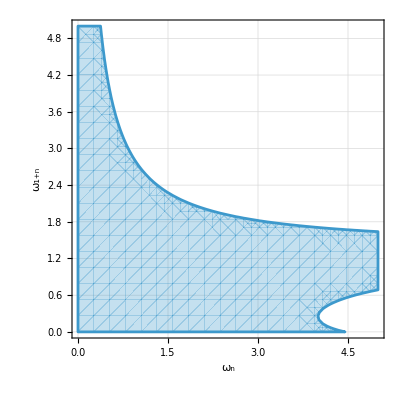

```mathematica
RegionPlot[stabl,{Subscript[ω, n],0,5},{Subscript[ω, n+1],0,5},FrameLabel->{Subscript[ω, n], Subscript[ω, n+1]},RotateLabel->False,GridLines->Automatic]
```